# What is money?

Are local currencies the ...

Leanne Ussher, Jun. 24,  2018

Community Currencies

Write a 3-5 sentence basic introduction of the topic, particularly why it's interesting. Note that the title should be as straightforward as possible (Rhythmic Timelines, not: Sonifying Clave son – Exploring Musical Rhythm), so the introduction provides the opportunity to elaborate and engage the reader. Don't make the subjects overly general—have them match the specificity of the content.

## Money

Start by explaining the basics ...

A common definition of fiat money is:

```mathematica
Entity["Word","fiat money"][EntityProperty["Word","Definitions"]]
```

{{fiat money,Noun}→money that the government declares to be legal tender although it cannot be converted into standard specie}

Fiat Currency is an IOU (I owe you). It consists of 1) federal reserve notes (green backs) in circulation and 2) bank deposits. In all cases these are IOUs. That are created from nothing (meaning of Fiat) by either the Federal reserve in the former, and banks in the latter. When we use the term IOUs we mean that the  Federal reserve or Bank has a debit or liability and the public has the credit or asset. This money which is held outside of the Federal Reserve System is known as outside money.  Typically the stock of money is measured as M1, (1+2).  A plot of the stock of money or M1 over time is below. This is an open domestic network where US dollars circulate overseas and back again. Money is endogenous and is not under under control of any entity (which shall discuss this later).

```mathematica
WolframAlpha["plot money supply m1","PodIDs"]
```

{Input,Result,History:MoneySupply:EconomicData,TimeSeriesOperator:ChangeRate:MoneySupply:EconomicData,TimeSeriesOperator:YearOverYearChangeRate:MoneySupply:EconomicData,MoneySupplyComponents:EconomicData}

```mathematica
WolframAlpha["plot money supply m1",IncludePods->{"History:MoneySupply:EconomicData"}]
```

WolframAlphaQueryResults

M0  (M zero) or inside money, is another kind of money that represents IOUs from the Fed to commercial banks, where banks hold deposits with commercial banks. This is a closed network that only circulates around these banks and the Fed controls the supply of M0.

## Velocity of Fiat Money

Each time money circulates (money times the number of transactions) it is in exchange for goods or services (price times quantity) we can write this as an equation:

M.V = P.Y

WolframAlphaQueryResults

[length] [time]^-1

The circulation of money is easiest to understand in a closed network with trade, and a source and a sink. This can be  shown by this simple flowgraph [But it doesn’t add up]. When the government spends (by printing money), it injects 15 units of cash into the network. These 15 units can circulate around the network from node to node, and at each point the money is distributed or circulates through the system.  (source and sink are both the government)

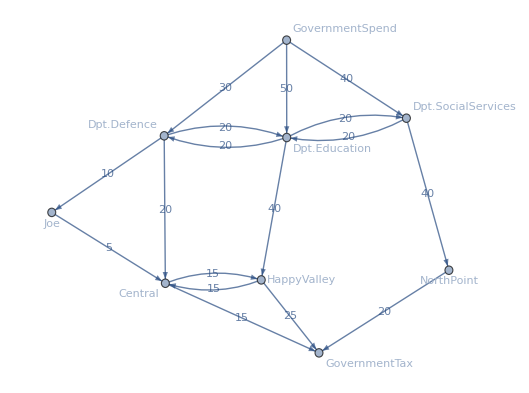

```mathematica
h
```

```mathematica
Total[PropertyValue[{h,#},EdgeCapacity]&/@EdgeList[h]]
```

405

In this case we have the following transactions, giving us a total number of transactions

Flows

Government Spending | 120
M.V | 405
Leakages | 60
Taxes | 60

This simplistic network of monetary circulation is a closed(?) network can represent the flow or M.V in the network where money is ‘conserved’. There is a source here, which is when the government spends, and there are a number of sinks, which is when the government taxes, but there is also some other sinks which we call leakages such as:

Leakages

Joe | 5
NorthPoint | 20
Happy Valley | 15
Dpt.Ed | 10
Central | 10

Alternatively there can be sinks in the system that do absorb money. There can pool up in nodes, or simply leave the system through imports. Thsi reduces circulation

Always have code text as a lead-in to code that follows, to concisely indicate what it does:

```mathematica
Code (* demonstrate a general case*)
```

## A Local Currency

Or show an example of application ...

Another way to start an exposition, or to expand on the basics, is to provide an example showing the application of the topic. The example might be something you arrive at by the end of the exposition, repeating that conclusion here is acceptable if it's reasonably self-contained. It might also be an example a problem scenario and the exposition explains a solution.

Always have code text as a lead-in to code that follows, to concisely indicate what it does:

```mathematica
Code (* demonstrate a specific application *)
```

```mathematica
Import[NotebookDirectory[]<>"schumacher_data2.csv"]
```

```mathematica
flow=FindMaximumFlow[{{1,2},{3,4}},1,2,"OptimumFlowData"]
```

OptimumFlowData[…]

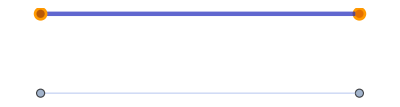

```mathematica
flow["FlowGraph"]
```

```mathematica
AdjacencyGraph[{{7,0,0,0,11,0,0,0,0,0,0,0,0,6,8,0,0,0,0,0,0,10,0,12,0,0,0,0,0,0,0,0,0,0,17,0,0,0,0,0,9,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,3,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,2,0,0,0,0,0,0,2,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,4,0,458,0,0,0,0,24,0,2,10,4,3,0,27,1,0,0,0,45,5,15,0,12,5,2,9,49,0,0,0,0,27,0,0,0,34,3,8,0,0,7,3,0,0,0},{0,1,0,0,1,15,0,0,0,3,0,0,0,9,4,2,7,3,0,0,0,6,0,15,0,0,15,8,4,4,0,0,0,0,28,1,0,2,1,4,8,1,1,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,2,2,0,0,5,7,0,4,2,91,6,0,7,3,0,0,0,6,1,55,0,1,0,0,0,11,0,0,0,0,23,0,0,0,12,0,1,2,0,11,0,0,0,0},{0,0,0,0,13,0,0,0,0,48,0,3,5,0,2,10,0,4,6,0,0,16,0,0,0,0,12,0,2,6,0,0,0,0,5,0,0,29,0,0,4,6,0,10,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,0,0,0,19,4,10,0,0,3,2,0,0,0,2,0,0,0,0,0,0,0,0,18,0,0,0,0,0,0,3,0,0,28,0,0,0,0,0,0,0},{0,0,0,0,7,0,0,1,1,0,0,40,42,9,0,0,2,0,0,0,0,2,0,2,0,0,0,0,0,0,0,0,0,0,2,2,0,1,0,1,0,3,0,0,0,0,0,0},{0,2,0,1,9,1,0,0,2,23,0,0,14,511,10,0,0,7,0,0,0,27,3,61,0,17,6,2,5,19,8,0,0,0,39,8,0,0,64,7,2,8,2,22,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,4,45,0,0,0,0,4,0,0,0,0,0,1,0,0,0,0,5,0,2,0,0,0,0,5,0,1,2,1,3,0,0,0},{0,0,4,0,0,3,0,2,0,1,0,0,4,3,1,0,6,24,0,0,0,3,2,2,0,2,5,0,0,3,0,0,1,0,8,0,0,3,4,0,3,2,2,3,2,0,3,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,4,0,0,16,0,18,0,0,1,0,12,0,0,2,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,8,0,0,0,0},{0,0,0,0,5,0,0,0,0,0,0,0,5,5,9,0,0,0,0,0,0,0,0,3,0,50,0,0,0,0,0,0,0,0,16,12,0,0,0,0,0,0,0,9,0,0,0,0},{0,0,7,0,3,0,0,1,0,0,0,0,19,0,104,0,7,1,0,0,0,6,0,37,0,0,5,0,0,9,0,0,0,0,3,0,0,0,0,8,0,1,0,0,0,2,0,0},{0,1,12,0,13,0,0,0,1,22,0,3,4,21,17,0,10,11,0,0,0,381,1,14,5,33,31,12,0,7,0,0,0,0,42,0,0,1,3,1,0,13,16,41,3,2,0,0},{0,2,0,0,28,0,0,0,0,22,0,8,3,7,16,0,9,6,0,2,0,25,10,0,0,2,12,0,21,17,21,0,6,0,12,0,0,43,0,7,0,7,0,31,4,5,0,0},{0,0,0,0,25,3,0,0,0,28,0,4,20,76,3,0,0,10,0,9,0,28,0,223,57,54,20,0,10,1,0,0,5,0,32,0,0,0,53,5,46,10,10,27,6,2,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,18,0,0,0,0,28,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,4,0,8,3,0,0,2,21,0,0,11,15,4,15,5,4,0,0,0,29,0,16,0,16,82,0,0,10,0,0,3,0,46,0,0,16,20,12,13,12,0,10,2,0,40,0},{0,0,4,0,0,0,0,0,1,0,0,1,10,19,0,2,2,3,0,0,0,11,0,6,0,0,5,48,0,2,0,0,0,0,12,0,0,6,0,1,20,3,0,12,0,0,1,0},{0,0,0,10,0,0,0,0,0,0,0,9,0,2,0,0,0,0,0,0,0,0,0,0,62,0,0,0,34,5,0,0,0,0,1,0,0,0,0,3,15,3,8,0,0,0,0,0},{4,3,1,0,0,1,0,0,8,5,0,0,12,6,7,0,3,3,0,8,1,12,1,0,0,5,3,0,0,17,0,1,4,0,13,9,0,0,1,5,15,4,0,1,2,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,3,0,9,1,0,3,0,2,0,0,9,20,6,0,0,1,0,0,0,8,0,2,0,2,11,0,0,6,0,5,0,0,22,0,0,0,0,0,2,0,0,7,2,0,0,0},{0,1,3,0,9,0,0,0,1,8,0,0,2,5,0,0,0,1,0,0,0,4,0,2,0,8,7,0,0,17,0,0,44,0,11,0,0,0,0,0,9,0,0,0,1,2,0,0},{0,11,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,19,0,98,14,0,0,2,45,0,23,43,37,23,0,0,16,25,22,1,127,8,48,37,32,51,9,25,29,20,0,19,0,1322,25,0,13,65,25,17,39,45,16,17,17,6,0},{0,0,0,0,6,0,0,0,0,2,0,0,12,0,0,0,7,0,0,0,0,0,0,2,0,11,0,0,0,0,0,0,0,0,5,3,0,0,0,0,18,5,7,17,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6,0,0,0,0,0},{0,1,0,0,36,0,0,0,5,36,0,123,7,28,17,0,7,1,0,0,0,26,1,8,16,94,19,6,3,24,19,0,0,0,39,5,0,5,404,12,3,10,0,15,6,6,3,0},{0,0,0,0,0,1,0,0,0,2,0,0,2,0,9,0,2,0,0,0,0,0,0,3,0,0,12,0,0,0,0,0,0,0,4,0,0,6,0,5,1,0,9,2,0,0,0,0},{0,0,0,0,0,0,0,5,0,5,0,0,0,23,3,0,0,9,0,0,0,10,0,0,0,14,10,0,0,0,5,0,1,0,58,0,0,21,0,0,114,1,11,7,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,14,0,4,5,0,0,2,0,0,0,0,0,26,0,0,2,0,0,0,0,0,0,0,0,0,0,0,1,5,0,56,0,4,0,0,0,0},{0,1,0,0,3,0,0,0,2,6,0,0,1,6,0,0,30,4,0,0,0,20,0,0,0,0,0,0,8,1,0,0,4,0,5,2,0,0,0,0,0,0,2,0,0,0,0,0},{0,0,0,0,10,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,26,0,0,0,0,0,0,0,0,15,0,0,0,6,0,3,0,3,3,0,11,0,0},{0,0,9,0,10,0,0,0,2,0,0,19,12,14,0,0,0,0,0,0,0,14,9,7,0,0,4,0,9,10,4,0,0,0,26,0,0,0,2,11,0,2,0,6,33,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,14,0,8,0,0,0,0,0,0,0,32,0,0,0,19,2,0,0,0,0,0,0,0,7,0,0,0,0,0,0,0,0,0,0,0,40,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}]
```

-Graphics-

```mathematica
g=%;
```

```mathematica
CommunityGraphPlot[SimpleGraph[g,VertexLabels->vertexNames]]
```

-Graphics-

```mathematica
CommunityGraphPlot[SimpleGraph[g]]
```

-Graphics-

```mathematica
nameList=Flatten[Import[NotebookDirectory[]<>"schumacher_data_names.csv"]]
```

{Animal Presence,Baker's wife,Barrington Ballet,Beckwhith's Glass,Berkshire Child,Berkshire Coffee,Berkshire Craft,Berkshire Cupboard,Bill's Pharmacy,Byzantium,Cabinet Works,Caligari's,Captain Toss,Carr Bros HDWE,Castle St. Café,Harry Conklin,Crystal Essence,Daily Bread,decades,Diva,Dolby Florist,EverGreen,Farshaw's,Frames on Wheels,Galeria Arriba,Gans Appliance,Gatby's,Gorham & Norton,Harland Foster,Herbert's Shoes,Home Textures,Impoco's Video,Initially Yours,Inn at Green River,Jack's,Jillifers,Jodi's,Kahn's,Krol Jewelers,La Tomate,Lamplighter,Laramee Cleaners,Leatherwoods,Main st Clothing,Manhattan Pizza,Mamphis Hair,Mill River Studio,Monument Mt}

```mathematica
vertexNames=Flatten[Position[nameList,#]][[1]]->#&/@nameList
```

{1→Animal Presence,2→Baker's wife,3→Barrington Ballet,4→Beckwhith's Glass,5→Berkshire Child,6→Berkshire Coffee,7→Berkshire Craft,8→Berkshire Cupboard,9→Bill's Pharmacy,10→Byzantium,11→Cabinet Works,12→Caligari's,13→Captain Toss,14→Carr Bros HDWE,15→Castle St. Café,16→Harry Conklin,17→Crystal Essence,18→Daily Bread,19→decades,20→Diva,21→Dolby Florist,22→EverGreen,23→Farshaw's,24→Frames on Wheels,25→Galeria Arriba,26→Gans Appliance,27→Gatby's,28→Gorham & Norton,29→Harland Foster,30→Herbert's Shoes,31→Home Textures,32→Impoco's Video,33→Initially Yours,34→Inn at Green River,35→Jack's,36→Jillifers,37→Jodi's,38→Kahn's,39→Krol Jewelers,40→La Tomate,41→Lamplighter,42→Laramee Cleaners,43→Leatherwoods,44→Main st Clothing,45→Manhattan Pizza,46→Mamphis Hair,47→Mill River Studio,48→Monument Mt}

```mathematica
f["FlowGraph"]
```

{200.,200.,200.,200.,200.,200.,200.,200.,200.,200.}[FlowGraph]

```mathematica
NotebookDirectory[]
```

```mathematica
"/Users/leanne/Documentsn=/GitHub/Summer2018Starter/Essay/"
```

## Section Header

Add more sections as needed to explain the topic....

Section names, the total number of sections, and section organization will differ based on the topic.

Here are some ideas for sections you might consider:

history/origins

derivation

applications

common misunderstandings

recent developments

unanswered questions

## Further explorations

Name of a related topic for exploration

Name of another related topic for exploration (repeat as needed)

## Author contact information

emailaddress@author.com

(We recommend using your wolfram ID, but any address where you would like to be contacted about this publication should work.)

## Guidelines for the Author

### Image

Try to use images created in the Wolfram Language as much as possible

If an external image is the only way to go, use Import to get the image into the notebook and reverse close the In/Out cell-group  to hide the input cell.

### Text

Use minimal text in small pieces to explain the topic and transition between pieces of code. One or two lines of text at a time should suffice.

Sub-guideline two

### CodeText

Before each line of code, add a single line in CodeText style, as a lead-in, to say what the code that follows will do.

End this line with a colon

Make a map of Monaco:

```mathematica
GeoGraphics[Entity["Country","Monaco"]]
```

-Graphics-

### Code

Keep code simple and straightforward; code cell should be at most 3 lines long

Breakup complicated lengthy code into multiple segments and separate with CodeText lead-ins explaining each segment

Try to create simple visualizations whenever possible to illustrate the topic and add visual interest

Extra code (for example, visualization options to simply make the output look pretty) can be distracting and take away focus from the main functionality. Either avoid these or use Iconize to hide them.

Instead of

```mathematica
Plot[Sin[x], {x, 1, 10}, PlotStyle -> {Red, Dashed, Thick}]
```

Use

```mathematica
Plot[Sin[x],{x,1,10},]
```

If using a Manipulate, remember to set SaveDefinitions->True, if it refers to definitions not contained within it. This will allow the Manipulate to work without having to re-evaluate the notebook, for every new session.

Include Data Repository

Include Function Repository (mention coming soon)